# Avlang — Generating

I’m computationally generating words that are the “average” of the same word in a bunch of different languages. I’m looking at the pronunciations and spelling of different words. Is there any way to generate an “average” word given the same word in two languages? Let’s start with the Spanish and French translation of “fish”.

```mathematica
KEYWORD="sun"
```

sun

```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation[KEYWORD, All]];
```

```mathematica
Iconize[rawTranslations]
```

```mathematica
translatedList = Transliterate[Values[rawTranslations]]
```

{tai yang,surya,sol,solnce,matahari,sol,suryya,shams,matahari,ri,soleil,Sonne,swrj,srengenge,gunes,nuryudu,surya,mat troi,taeyang,katiravan,phraxathity,sole,tai yang,jua,aftab,surya,slonce,sonce,rana,taiyang,suran,surya,နေ,suryya,tai yang,swrj,panonpoe,suraja,suraja,gunəs,soare,araw,zon,sj, as,adlaw,anwu,ጸሐይ,surya,suryya,nap,mata are,របហឤតិត្យ,suraja,naange,suraja,qorrax,elios,sunce,slunce,zuva,aftab,gyangjngoenz,ilanga,dzuwa,so,sonca,sl"nce,sol,owia,kүn,init,kүn,Jzuba,ilanga,adlaw,mwese,arev,sol,koas,matoari,gun,sunce,si'iha canda,son,sol,aurinko,sms,slnko,rwch, pytap,izuba,sol,aphataba,ཉི་མ་,letsatsi,eguzki,mze,letsatsi,naaj,saldang,mata esso,dyambu,sol,zwn,kүn,saule,mata uroe,asista,wayno,suno,sonce,arrishsho,ҡoas,hevel,lilanga,mataallo,sonce,risase,ilanga,saule,la'a,muhanya,akolong,sudrya,heol,paike,grian,duvha,malha,anchu,inti,ndama,ci,soley,nlo-djop,winnig,aptap,la,utin,adlaw,xemx,kүn,la,souleu,sondi,matanisiga,sol,solo,si,kunes,johonaa'ei,raa,gun,q'ij,zətu,slonce,araii,kun,sua,sol,enjuba,sulegl,dylaca,k'in,hatӆ,tirkytir,suryah,kuarahy,siun,hash nittak aya,hotal,tijkytij,wira,sams,kece,kolon,mataniari,k'eң,hasi,sams,Phoebus,inti}

```mathematica
Length[translatedList]
```

181

```mathematica
AverageWord[word_String]:=Module[{words,charLists,avgLen,paddedLists,transposed,mostFreqChar,averageWord},words=Transliterate[Values@KeyValueMap[#1->First[#2]&,WordTranslation[word,All]]];charLists=Characters/@words;avgLen=Round[Mean[Length/@charLists]];paddedLists=Map[Function[chars,If[Length[chars]>avgLen,Take[chars,avgLen],PadRight[chars,avgLen,"-"]]],charLists];
transposed=Transpose[paddedLists];mostFreqChar=Map[Function[col,Module[{counts,filtered},filtered=DeleteCases[col,"-"];If[filtered==={},"-",counts=Tally[filtered];
First@First@SortBy[counts,-Last[#]&]]]],transposed];averageWord=StringJoin[DeleteCases[mostFreqChar,"-"]];
averageWord]
```

```mathematica
AverageWord[KEYWORD]
```

sanaa

```mathematica
translatedList=Select[translatedList,StringMatchQ[#,CharacterRange["A","z"]..]&];
```

```mathematica
translatedList
```

{surya,sol,solnce,matahari,sol,suryya,shams,matahari,ri,soleil,Sonne,swrj,srengenge,gunes,nuryudu,surya,taeyang,katiravan,phraxathity,sole,jua,aftab,surya,slonce,sonce,rana,taiyang,suran,surya,suryya,swrj,panonpoe,suraja,suraja,soare,araw,zon,adlaw,anwu,surya,suryya,nap,suraja,naange,suraja,qorrax,elios,sunce,slunce,zuva,aftab,gyangjngoenz,ilanga,dzuwa,so,sonca,sol,owia,init,Jzuba,ilanga,adlaw,mwese,arev,sol,koas,matoari,gun,sunce,son,sol,aurinko,sms,slnko,izuba,sol,aphataba,letsatsi,eguzki,mze,letsatsi,naaj,saldang,dyambu,sol,zwn,saule,asista,wayno,suno,sonce,arrishsho,hevel,lilanga,mataallo,sonce,risase,ilanga,saule,muhanya,akolong,sudrya,heol,paike,grian,duvha,malha,anchu,inti,ndama,ci,soley,winnig,aptap,la,utin,adlaw,xemx,la,souleu,sondi,matanisiga,sol,solo,si,kunes,raa,gun,slonce,araii,kun,sua,sol,enjuba,sulegl,dylaca,tirkytir,suryah,kuarahy,siun,hotal,tijkytij,wira,sams,kece,kolon,mataniari,hasi,sams,Phoebus,inti}

```mathematica
SYLLABLECOUNT=Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
```

2

```mathematica
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
```

NetGraph[…]

```mathematica
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
```

```mathematica
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]]
```

NetGraph[…]

```mathematica
results = 
 NetTrain[net, <|"Input" -> translatedList|>, All, LossFunction -> "Loss", 
  MaxTrainingRounds -> 300]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1500  rounds:300  time:58s  examples/s:835
data | ,,  training examples:151  processed examples:48000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:8.14×10^-1  error:27.1%
 | 
 | ]

```mathematica
trainednet=results["TrainedNet"]
```

NetGraph[<4>, <6>]

```mathematica
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}]
```

NetChain[<3>]

```mathematica
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
```

```mathematica
newAvgWords=Sort@Complement[Table[wordz[],20],translatedList]
```

{adla,gune,gyan,Jzub,kolo,sin,slon,sunc,sura,sury,taey,winn}

```mathematica
WordCloud[StringTake[newAvgWords, 1]]
```

-Graphics-

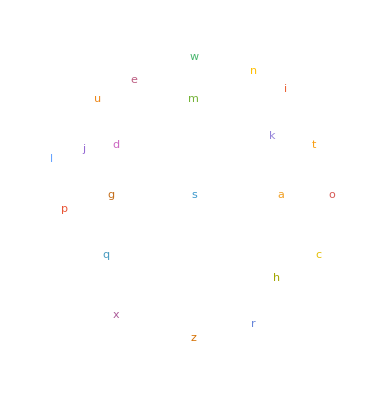

```mathematica
WordCloud[StringTake[translatedList, 1]]
```

```mathematica
positionedDigrams=Flatten[Table[If[StringLength[word]>=pos+1,{pos,StringTake[word,{pos,pos+1}]},Nothing],{word,translatedList},{pos,StringLength[word]-1}],1];
```

```mathematica
Iconize[positionedDigrams]
```

```mathematica
groupedByPosition=GroupBy[positionedDigrams,First->Last];
```

```mathematica
Iconize[groupedByPosition]
```

```mathematica
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
```

```mathematica
Iconize[countsByPosition]
```

```mathematica
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[3]],{pos,Sort@Keys[countsByPosition]}]
```

{{so,su,ma},{ur,ol,on},{ry,ta,ra},{ya,ng,an},{ce,ya,ja},{ng,ar,ts},{si,ri,ng},{ge,an,hi},{it,oe,ga},{ty,en},{nz}}

```mathematica
generateWord[]:=Module[{numSyllables,selectedLists,syllables},numSyllables=SYLLABLECOUNT;
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]]

(*Example:generate 10 words*)
Table[generateWord[],{10}]
```

{suol,maon,suon,maol,suur,sour,sool,maur,suur,soon}

```mathematica
mostCommonByPosition=AssociationMap[ReverseSortBy[Normal[countsByPosition[#]],Last][[1]]&,Keys[countsByPosition]];
```

```mathematica
mostCommonByPosition
```

<|1→so→23,2→ur→16,3→ry→10,4→ya→8,5→ya→4,6→ng→4,7→si→3,8→ri→1,9→oe→1,10→ty→1,11→nz→1|>

```mathematica
digramsInOrder=Keys[mostCommonByPosition/@Keys[mostCommonByPosition]];
```

```mathematica
digramsInOrder
```

{so,ur,ry,ya,ya,ng,si,ri,oe,ty,nz}

```mathematica
words = Table[
   StringJoin @@ Take[digramsInOrder, n]
   , {n, Length[digramsInOrder]}
]
```

{so,sour,sourry,sourryya,sourryyaya,sourryyayang,sourryyayangsi,sourryyayangsiri,sourryyayangsirioe,sourryyayangsirioety,sourryyayangsirioetynz}

```mathematica
words[[4]]
```

sourryya

```mathematica
ReverseSortBy[Total /@ Merge[LetterCounts[#,2]&/@translatedList, Identity], Identity]
```

<|so→23,su→20,an→19,ol→17,ur→16,ya→15,ra→14,ta→13,on→13,ng→13,ry→11,nc→11,at→11,ce→10,ar→10,un→10,la→10,ri→9,le→9,ma→8,ha→8,ti→8,sa→8,si→7,lo→6,in→6,am→5,il→5,aj→5,ga→5,ko→5,ah→4,ms→4,en→4,gu→4,ir→4,sl→4,na→4,ja→4,aw→4,ap→4,aa→4,zu→4,ni→4,ba→4,as→4,ts→4,al→4,ul→4,is→4,yy→3,sh→3,ne→3,re→3,ge→3,es→3,ua→3,ab→3,ai→3,no→3,oe→3,oa→3,ad→3,dl→3,wi→3,ia→3,ub→3,au→3,ho→3,ku→3,ln→2,nn→2,sw→2,wr→2,rj→2,ud→2,du→2,ey→2,va→2,ph→2,ax→2,it→2,ju→2,af→2,ft→2,pa→2,rr→2,el→2,li→2,uv→2,wa→2,ca→2,se→2,ev→2,nk→2,et→2,eg→2,da→2,dy→2,bu→2,he→2,ke→2,nt→2,nd→2,ig→2,ky→2,yt→2,ij→2,ei→1,So→1,sr→1,nu→1,yu→1,ae→1,ka→1,av→1,hr→1,xa→1,th→1,hi→1,ty→1,iy→1,np→1,po→1,zo→1,nw→1,wu→1,qo→1,or→1,io→1,os→1,lu→1,gy→1,gj→1,jn→1,go→1,nz→1,dz→1,uw→1,ow→1,Jz→1,mw→1,we→1,to→1,sm→1,iz→1,uz→1,zk→1,ki→1,mz→1,ze→1,ld→1,mb→1,zw→1,wn→1,st→1,ay→1,yn→1,hs→1,ve→1,ll→1,mu→1,uh→1,ny→1,ak→1,dr→1,eo→1,ik→1,gr→1,vh→1,lh→1,ch→1,hu→1,ci→1,pt→1,ut→1,xe→1,em→1,mx→1,ou→1,eu→1,di→1,ii→1,nj→1,gl→1,yl→1,ac→1,rk→1,hy→1,iu→1,ot→1,jk→1,ec→1,Ph→1,eb→1,us→1|>

```mathematica
audioSpanish=AudioTrim[SpeechSynthesize[WordTranslation["fish", "Spanish"][[2]]]]
```

```mathematica
audioFrench = AudioTrim[SpeechSynthesize[WordTranslation["fish", "French"][[1]]]]
```

```mathematica
audioEnglish=AudioTrim[SpeechSynthesize[WordTranslation["fish", "English"][[1]]]]
```

```mathematica
audioGerman =AudioTrim[SpeechSynthesize[WordTranslation["fish", "German"][[1]]]]
```

```mathematica
enc=NetEncoder[{"AudioSpectrogram"}]
```

NetEncoder[…]

```mathematica
generateSpectrogram[a_]:=ColorNegate[ImageReflect[Image[Normal[Spectrogram[a][[1,1]]]]]]
```

```mathematica
ss = enc[audioSpanish]
```

```mathematica
ss2=generateSpectrogram[audioSpanish]
```

-Graphics-

```mathematica
ss3=ShortTimeFourier[audioSpanish,Automatic,Automatic,HannWindow]
```

ShortTimeFourierData[…]

```mathematica
ss3Data=Values[Normal[ss3][[1]][[1]]]
```

```mathematica
Spectrogram[ss3]
```

-Graphics-

```mathematica
Dimensions[ss3Data]
```

{163,256}

```mathematica
Spectrogram[ss3]
```

-Graphics-

```mathematica
Audio[InverseShortTimeFourier[ss3]]
```

```mathematica
WSRP24
```

```mathematica
sf = enc[audioFrench]
```

```mathematica
sf2=generateSpectrogram[audioFrench]
```

-Graphics-

```mathematica
sf3=ShortTimeFourier[audioFrench,Automatic,Automatic,HannWindow]
```

ShortTimeFourierData[…]

```mathematica
sf3Data=Values[Normal[sf3][[1]][[1]]]
```

```mathematica
Dimensions[sf3Data]
```

{166,256}

```mathematica
snew=Image[ImageAdd[ImageRotate[Image[ss]], ImageRotate[Image[sf]]]]
```

-Graphics-

```mathematica
-Graphics-ShortTimeFourier[audioSpanish,Automatic,Automatic,HannWindow]
```

-Graphics- ShortTimeFourierData[…]

```mathematica
AveragePaddedArrays[array1_,array2_]:=Module[{maxRows,maxCols,padded1,padded2,dims1,dims2},
dims1=Dimensions[array1];
dims2=Dimensions[array2];
maxRows=Max[dims1[[1]],dims2[[1]]];
maxCols=Max[dims1[[2]],dims2[[2]]];
padded1=PadRight[array1,{maxRows,maxCols},0];
padded2=PadRight[array2,{maxRows,maxCols},0];
(padded1+padded2)/2]
```

```mathematica
averageSTFT=AveragePaddedArrays[ss3Data, sf3Data]
```

```mathematica
d = InverseShortTimeFourier[averageSTFT]
```

```mathematica
Audio[d, SampleRate->16000]
```

```mathematica
Spectrogram[d]
```

-Graphics-

```mathematica
Spectrogram[Audio[LowpassFilter[d, 0.5], SampleRate->16000]]
```

-Graphics-

```mathematica
Audio[LowpassFilter[d, 0.5], SampleRate->16000]
```

```mathematica
a=InverseSpectrogram[ss2]
```

```mathematica
Spectrogram[audioSpanish]
```

-Graphics-

```mathematica
Spectrogram[a]
```

-Graphics-

```mathematica
b=InverseSpectrogram[ImageRotate[Image[enc[audioSpanish]]]]
```

```mathematica
Spectrogram[b]
```

-Graphics-

```mathematica
c=InverseSpectrogram[snew]
```

```mathematica
Audio[a, SampleRate->16000]
```

```mathematica
Audio[b, SampleRate->16000]
```

```mathematica
Audio[c, SampleRate->16000]
```

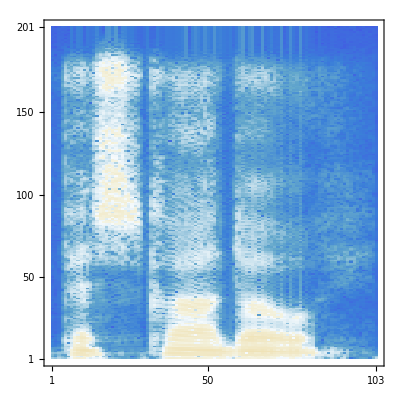

```mathematica
MatrixPlot[Log[Transpose[ss]], DataReversed->{True, False}, AspectRatio->1]
```

```mathematica
avgSpectrogram=(ArrayPad[ss,{{0,1},{0,0}}]+sf)/2;
```

```mathematica
Audio[InverseSpectrogram[avgSpectrogram], SampleRate->16000]
```

```mathematica
Dimensions[ss]
```

{128,201}

```mathematica
words={WordTranslation["light", "English"][[1]], WordTranslation["light", "French"][[4]], WordTranslation["light", "Spanish"][[5]]}
charLists=Characters/@words
maxLen=Max[Length/@charLists];
paddedLists=PadRight[#,maxLen,"-"]&/@charLists;
transposed=Transpose[paddedLists];
transposed
mostFreqChar=Map[Function[col,Module[{counts,filtered},filtered=DeleteCases[col,"-"];
If[filtered==={},"-",counts=Tally[filtered];
First@First@SortBy[counts,-Last[#]&]]]],transposed];
mostFreqChar
averageWord=StringJoin[DeleteCases[consensusLetters,"-"]]
```

{light,lumière,luz}

{{l,i,g,h,t},{l,u,m,i,è,r,e},{l,u,z}}

{{l,l,l},{i,u,u},{g,m,z},{h,i,-},{t,è,-},{-,r,-},{-,e,-}}

{l,u,g,h,è,r,e}

lughère

```mathematica
net=NetModel["GloVe 100-Dimensional Word Vectors Trained on Tweets"]
```

EmbeddingLayer[<>]

```mathematica
vecs=Normal@NetExtract[net,"Weights"][[1;;-2]];
```

```mathematica
word2vec=AssociationThread[words->vecs];
```

```mathematica
Nearest[word2vec,word2vec["poisson"],5]
```

{poisson,poissons,d'avril,signe,masque}

```mathematica
extractor=NetChain[{NetModel["Whisper-V1 Multilingual Turbo"],AggregationLayer[Max,1]}][AudioPartition[#,30][[1]]]&
```

NetChain[{NetModel[Whisper-V1 Multilingual Turbo],AggregationLayer[Max,1]}][AudioPartition[#1,30]⟦1⟧]&

```mathematica
audios={audioSpanish->"Spanish",audioFrench->"French",audioEnglish->"English", audioGerman->"German" };
```

```mathematica
(* FeatureSpacePlot[audios,FeatureExtractor->extractor,LabelingFunction->Callout]*)
```

-Graphics-

```mathematica
(* featuresEnglish = extractor[audioEnglish]
featuresGerman = extractor[audioGerman]
featuresFrench = extractor[audioFrench]
featuresSpanish = extractor[audioSpanish] *)
```

{0.774171,0.719631,0.759881,0.631769,0.826635,0.908477,0.732558,1.12869,1.31293,0.98251,0.800492,1.00817,0.808665,0.776203,0.820396,1.24126,1.02109,0.954736,1.24192,1.23756,1.07509,1.16689,0.849514,0.81745,0.709537,0.726202,0.739852,0.790792,0.994964,0.871079,0.984711,0.761131,0.746905,0.786765,1.41789,0.997074,0.760269,0.848729,0.862149,0.880143,1.11858,1.06614,0.939398,0.947875,0.812391,1.33791,1.02307,0.956568,1.24641,1.06704,0.88115,0.791525,1.21875,0.806163,1.42222,1.23695,1.37143,1.12987,1.3487,0.927695,1.14026,2.83735,1.05268,1.18407,1.05678,1.09039,1.012,1.21731,0.815894,1.34669,0.771008,1.16941,0.925183,0.824055,1.1263,0.912548,1.22294,1.00131,0.820401,0.984049,0.920434,0.849586,0.828685,1.0491,1.16012,0.882728,0.964341,0.789098,0.944518,1.01947,1.88916,0.670617,0.909887,0.460764,0.975489,1.10799,0.952197,0.800464,1.14472,0.952666,1.28195,1.13514,0.849474,0.830162,0.728182,0.94601,1.06894,0.755903,1.21056,0.891513,0.989706,1.29011,0.993587,1.08718,1.04836,0.872235,2.22002,1.13155,1.07711,0.83807,1.04337,0.811216,1.17395,1.2283,0.789591,0.962139,1.03846,0.797361,0.692767,0.719227,1.01761,1.08332,0.854921,0.939724,0.763391,1.1069,0.935704,1.01166,0.808471,0.981373,1.14912,1.31907,1.14064,1.11149,0.916265,0.845951,0.995178,0.99077,0.91932,0.882433,0.916839,3.95378,0.812488,0.896717,1.10472,0.900737,1.77652,0.880935,1.5057,1.00717,1.72737,1.11086,1.0067,0.833267,0.853429,0.926996,0.967287,0.8444,0.900422,0.901072,1.14714,1.49388,0.872511,0.977507,1.24687,1.15786,1.21608,1.13684,1.10841,0.857357,1.5002,0.84698,4.36485,0.707804,1.03424,1.281,1.26359,0.562464,0.685724,1.18359,1.24012,1.01715,1.18282,1.18458,1.46351,1.38591,1.13588,1.41977,1.54343,1.2208,1.31269,1.06296,1.23885,1.03321,0.805007,0.897218,0.966484,0.960517,1.24427,0.791861,0.733285,0.769227,0.744786,0.874165,1.09789,1.21534,1.39405,0.97601,0.999661,1.03997,1.26734,0.855351,1.00298,1.49755,0.880764,0.700711,1.05522,2.73339,1.1078,1.35822,1.15159,2.61959,0.979029,0.959016,1.16206,1.20754,1.15877,1.07653,0.876551,1.2219,1.17011,1.10862,1.13205,0.935506,1.05667,0.913634,0.931257,1.26236,1.20048,1.01232,0.976496,0.89171,0.984467,0.850698,1.23368,0.785955,0.932946,1.32042,1.16503,1.0216,0.90074,0.723188,1.33732,0.946869,0.946755,1.18413,1.39972,0.818821,1.00563,0.834069,0.811835,1.19667,1.17418,1.17392,1.21183,0.896576,1.19946,1.09403,0.859106,0.613346,0.673695,0.998583,1.19621,1.06966,1.20451,0.843783,1.34844,1.07691,0.968859,1.21696,0.974054,0.869834,0.948008,0.865781,1.22174,0.868728,0.875825,0.812745,1.28526,1.3875,0.822806,0.951218,0.815463,1.33362,0.988441,0.654523,1.3175,1.06002,1.17786,1.13442,1.14322,0.753428,0.83312,1.28272,0.974636,0.950766,1.01945,1.49688,2.09519,7.14439,0.677672,0.843516,1.13583,1.16861,0.794248,1.00752,1.18549,0.949175,3.03925,0.596643,0.879087,1.16626,0.800682,0.893409,0.872077,0.80745,1.12855,1.22194,0.726912,0.883563,0.882699,1.07033,0.902287,1.0686,1.09203,0.80273,0.92066,0.845005,0.846505,1.12455,1.0195,1.374,0.993206,1.05549,1.11092,1.02761,0.818848,1.05811,1.23259,1.11061,0.765214,1.26545,1.23808,1.09478,1.23003,1.12748,0.756889,0.849223,1.29104,1.25479,1.00318,0.954807,1.01721,0.996403,1.16868,0.865875,1.12312,0.833862,1.40179,1.30522,0.882799,1.26205,1.02847,1.49417,0.76808,1.15658,0.986223,1.18168,1.07764,0.784144,0.946799,2.04992,2.47139,1.05041,1.29203,0.714365,0.837577,0.865095,1.14555,0.46599,0.78455,0.799418,0.654669,2.13231,0.935378,1.07497,1.00971,1.06909,0.847029,1.05505,0.992838,0.953241,1.0781,0.749228,0.886774,1.38448,1.04287,1.53015,1.05023,1.02124,1.03245,1.04131,0.69408,0.944735,0.921468,0.814733,1.10699,1.00371,0.778832,1.21159,1.04961,0.950549,1.07321,1.04857,1.30395,1.03112,0.841323,0.923506,1.10646,0.848144,1.47911,1.0057,0.749235,0.775109,1.22502,1.73655,1.03084,0.767805,1.26214,0.898026,1.22355,1.37857,0.970834,1.08986,0.801519,0.696346,0.984541,1.33219,0.96942,0.927446,1.0283,1.09415,1.09794,0.779003,0.713928,0.973576,1.75645,0.86741,1.12234,1.08616,1.02473,0.782065,1.23058,0.963553,1.28104,0.850468,1.17087,1.95644,0.882839,1.0385,0.97031,1.01275,1.03707,1.36735,0.996233,0.921538,1.05505,0.587759,0.926376,0.715256,0.848553,0.860826,0.728148,0.685717,0.903696,0.652255,1.29265,1.037,1.20992,1.14958,1.10413,1.21715,1.09698,1.25163,0.94781,0.870773,0.844885,0.850205,1.02716,1.11393,0.809835,0.578801,0.71218,0.821288,0.731185,0.864699,0.875148,0.912038,1.03048,0.656933,0.907672,1.03196,1.21623,0.926972,0.69671,0.889706,0.845285,1.09783,0.745686,0.817986,0.865563,0.955558,1.08323,0.963854,1.15851,1.21491,0.839368,1.22624,0.879907,1.33218,0.914654,1.13835,0.878495,0.926492,1.61487,1.09669,0.829938,1.43707,0.900364,1.1404,1.23789,0.91401,1.6487,0.879659,0.936067,1.05732,0.803254,0.814707,0.955815,0.819083,1.02824,1.02247,0.945273,0.796214,0.778401,0.79894,0.765518,0.737641,0.702534,0.64944,0.759994,0.926202,0.888147,0.997975,1.12234,0.991677,1.07681,1.01206,0.876681,0.76884,1.09749,0.94063,0.867904,1.26794,0.859735,0.889168,1.60387,0.968983,1.1462,1.24847,0.79722,0.90604,0.983415,0.842439,2.4449,1.11582,0.74686,0.785294,0.835451,0.777304,0.83285,0.856985,1.10916,0.960085,0.879053,0.797543,0.917137,1.02444,1.47686,0.717521,0.964563,1.29241,0.713599,0.97693,0.947482,1.2331,0.940294,1.30124,1.05749,1.12697,1.11368,0.953545,0.539656,1.42747,0.827928,1.18152,0.6019,1.10897,1.00913,1.02497,1.21278,0.864258,0.903078,1.04463,1.10109,10.1706,0.7555,0.903892,1.1004,1.20799,1.34405,0.960052,1.12844,0.888428,1.61946,0.898774,0.949072,0.815217,1.00247,0.764991,0.811053,1.37419,0.81998,0.980964,1.00976,1.02669,1.24938,0.780028,0.682241,0.886279,0.955452,0.890462,1.02984,1.08213,0.947393,0.785514,0.782921,1.25473,0.719296,1.11736,1.04514,0.84177,0.839864,1.33442,0.771167,0.975462,0.996912,0.795408,0.968422,0.763428,1.17866,0.912981,0.981343,0.87941,1.5361,1.13017,1.05589,0.827125,1.28769,0.962403,1.12175,2.00043,0.940823,1.01958,1.26175,1.24022,1.21401,1.1578,0.92818,0.785182,0.863974,1.38851,1.18234,1.24755,0.845133,1.62421,0.698987,0.757864,0.672056,0.956592,0.855975,1.00127,0.795154,0.693583,1.13205,1.31245,1.20151,1.07399,1.11042,1.10178,0.941132,0.988483,0.880132,1.05422,1.33073,0.749423,0.76163,0.729287,1.22511,1.96547,1.19209,1.22299,1.22042,1.0961,0.909276,1.24448,1.117,0.90445,0.981596,1.15209,0.859964,0.877575,1.00923,0.97413,1.12067,1.04391,0.707949,1.11236,0.868843,0.977339,1.18575,1.18781,1.53844,1.10863,0.953091,1.31611,2.18489,1.04403,1.06279,1.05068,1.07042,1.18283,0.989853,1.41314,1.13963,1.03823,0.699952,0.880917,1.10697,1.25178,0.871068,1.02636,0.766088,0.926672,0.97271,0.888804,0.937002,1.28738,1.3034,0.911774,1.3155,0.937073,0.909152,1.02732,1.18943,0.2908,0.823092,0.982793,0.962224,1.32427,0.813633,0.880322,0.996707,1.47415,1.28913,0.931893,0.869244,0.734453,1.25838,0.995455,1.85467,0.910514,0.892151,1.16251,1.16886,0.840615,0.843404,0.882163,1.01659,1.10581,1.05677,1.03426,0.705085,1.02336,0.930129,1.18061,1.09275,1.08624,1.21017,1.32984,1.28721,1.11535,1.22646,1.20298,1.21417,0.70166,1.6282,1.08433,1.01696,0.919122,1.36764,1.02597,1.17057,1.29129,1.04877,1.1821,0.821109,1.21789,1.40865,1.05103,0.910787,1.22963,1.17983,0.734731,1.07172,1.13012,1.0407,0.983859,0.902877,0.939645,0.877282,0.938584,1.12427,1.17569,1.2897,0.973956,0.91399,0.673133,0.938426,0.957976,0.813637,1.23752,0.770731,0.923167,0.986979,1.19008,1.20411,1.07854,0.74437,0.939878,1.01335,0.870917,1.16377,0.875562,1.04951,1.00386,0.995598,1.24529,1.02198,1.41625,0.712914,0.844573,0.762549,1.00832,0.92143,1.0202,0.865117,0.742905,0.870959,1.41244,1.28718,1.05103,0.941998,1.04843,1.32618,0.900872,0.982817,0.869169,0.874319,0.834785,1.46701,0.991976,0.604456,1.2314,0.841993,0.972923,0.980275,1.33894,0.817146,0.720322,0.820751,1.22576,0.717749,1.20911,0.821371,1.59532,1.08991,1.21794,1.3803,0.946816,0.974136,0.998968,0.689222,0.793665,0.821681,1.17827,0.641201,1.47847,0.983398,1.09,0.953841,1.26466,1.04776,1.2203,0.64649,1.13949,0.888492,0.861697,1.18388,1.05632,1.11929,1.38061,0.823605,1.42209,1.00443,0.940914,0.874674,0.89353,1.19085,1.21419,1.19014,1.25947,1.01838,1.10464,0.834321,0.90694,0.92147,0.702558,1.00815,0.734766,1.05174,0.978437,1.18466,0.703371,0.950956,0.829652,1.19139,1.16362,0.868401,0.998248,1.17699,0.976961,1.28995,1.21867,0.68839,0.982411,1.0219,1.20564,0.856465,1.28542,0.998006,1.31499,1.23668,0.963873,1.0015,0.902853,1.37466,6.71967,4.72016,0.923654,1.06859,0.849374,1.05069,0.932201,1.59703,0.600782,1.09834,1.01498,1.17312,1.17578,0.936825,1.20702,1.19919,1.07891,1.07149,1.08128,1.13181,1.24358,1.3294,1.15699,0.84191,0.649885,0.752754,1.25393,0.880137,1.41087,0.944024,0.936037,1.04463,0.883959,0.84885,0.938178,1.1106,0.675765,1.10053,0.840627,0.832837,0.991671,1.07897,1.09444,1.93074,0.80715,0.786491,1.40871,0.991152,1.08525,0.939563,0.655746,0.846702,0.937492,0.733954,1.08385,1.04005,1.09286,0.976066,1.1262,0.94759,1.03841,1.20689,0.925057,1.1404,0.904874,0.824404,1.23423,0.870838,0.999422,0.931169,0.674098,1.15187,1.01,0.825931,1.16425,0.641211,1.13575,0.946972,1.30735,0.912731,0.864293,0.905395,0.771334,0.850719,0.963704,0.963299,0.850234,0.957232,2.91101,0.814573,0.951847,0.765108,0.815954,0.973988,1.03286,0.939314,0.842274,0.917163,1.04488,1.17626,1.01346,1.13187,1.02709,0.686672,0.88267,2.9815,1.14471,0.944178,1.0274,1.14753,1.29459,1.34102,1.20601,0.937701,1.13877,0.891185,0.772511,0.938589,1.02539,1.04278,1.08404,0.924782,1.1676,0.962019,0.940238,0.700984,1.0419,0.845078,1.00207,1.43299,0.968229,0.667403,0.833583,0.744544,0.88154,0.882751,0.714093,1.08146,0.991879,0.949925,1.17211,0.876462,0.920643,1.1219,0.874922,1.2597,0.956628,0.969148,1.03842,0.982584,1.04203,0.914642,1.45267,1.19536,0.815048,3.42772,0.977187,0.859617,1.00022,0.918433,1.41704,1.12303,2.41217,0.884584,0.917601,0.95063,0.968599,0.869241,0.726486,0.726394,1.00459,1.20054,0.992306,1.17684,0.957708,0.959122,1.26146,1.0474,0.940447,1.03708,1.10612,1.212,0.877735,0.832564,1.15396,0.833992,0.910857,0.905355,1.06224,0.603851,1.02588,1.38509,1.12017,0.962799,0.912599,1.00105,0.824467,1.20212,0.869862,1.078,1.11711,1.17642,0.801688,1.07102,0.731327,0.820472,1.49016,0.91778,0.994656,1.29975,1.27186,0.924591,1.07445,1.13998,0.909422,0.878539,1.11446,0.87464,0.665784,0.971,0.976044,1.15405,0.957882,1.02775,0.800808,1.06754,0.831219,0.64987,1.2683,0.897633,0.712936,0.822186,1.04636,0.855112,0.996836,1.6201,1.04871,1.07494,1.17433,1.01562,1.07332,0.804416,0.918498,1.38756,0.877248,1.05653,0.811352,0.829152,1.21265,0.982834,0.830737,1.01208,1.12846,0.860131,0.859137,0.880918,0.690392,1.47899,1.32432,0.965447,1.07035,1.28643,0.980371,1.30651,0.857588,0.958485,0.843879,1.09454,0.777596,0.801212,0.771688,1.50649,0.936251,1.21551,0.69713,0.788947,1.15962,1.27138,1.05127,1.19254,0.784851,1.15722,0.913139,0.691379,0.962296,0.965456,0.916523,0.902853,0.73759,1.03832,0.803088,0.972746,0.830981}

{0.781092,0.695251,0.756813,0.635694,0.852918,0.897548,0.700583,1.22312,1.33738,0.903965,0.826284,1.06561,0.794518,0.774506,0.855071,1.19929,0.92618,0.971971,1.32634,1.1837,1.08505,1.17804,0.856548,0.952087,0.655015,0.783279,0.721483,0.835519,1.01629,0.74727,1.06336,0.759319,0.732531,0.838994,1.39429,0.962379,0.759061,1.04474,0.930301,0.907232,1.23355,1.06637,1.0013,0.911981,0.703597,1.26446,1.00005,0.948665,1.33979,0.980249,0.92896,0.701055,1.39319,0.7987,1.37682,1.22611,1.32977,1.14123,1.54979,1.00074,1.08162,2.97088,1.24095,1.16705,0.901538,1.04655,0.983289,1.25254,0.898995,1.40881,0.788216,1.06644,0.939087,0.868369,1.20879,0.90077,0.918658,1.09524,0.827826,1.07345,0.948459,0.878173,0.842318,0.981736,1.31444,0.950958,0.879538,0.778132,1.08076,1.08057,1.89307,0.793656,0.935658,0.500394,0.954023,1.10061,1.02736,0.787184,1.16001,0.979058,1.32251,1.10465,0.857125,0.740415,0.907255,0.917716,1.22365,0.897915,1.21109,0.885762,1.03464,1.28071,0.898079,1.13167,0.969668,0.985315,2.45833,1.20285,1.00067,1.02009,1.15389,0.945398,1.24835,1.26392,0.911232,0.922846,1.13058,0.806577,0.74394,0.74529,1.07021,1.0851,0.836665,1.02038,0.670974,0.847771,1.00229,0.93697,0.653835,1.19509,1.16801,1.24346,1.17424,1.04498,0.98889,0.937167,1.07616,0.922555,1.00525,0.92542,0.949544,3.75766,0.81397,0.89057,1.02468,0.942295,1.69594,0.907256,1.57014,1.1009,1.70222,1.11827,1.09557,0.783381,0.883213,0.92389,0.995541,0.821231,0.876214,0.74771,1.193,1.45842,0.857438,1.03158,1.05436,1.15783,1.15001,1.13108,1.16956,0.843798,1.14616,0.771063,4.2162,0.734787,1.01746,1.17349,1.14674,0.711729,0.725207,0.997864,1.31974,0.991031,1.11243,1.12699,1.47468,1.21062,1.17695,1.41708,1.54944,1.22958,1.21584,1.11542,1.38075,1.01506,0.803424,0.810121,1.04762,0.968203,1.22464,0.805604,0.795364,0.788837,0.729161,0.920696,0.995823,1.3496,1.28782,1.0089,1.22462,1.11967,1.26851,0.754326,1.04745,1.2226,0.882055,0.717197,1.09405,2.72018,1.08739,1.36898,1.13637,2.57579,1.00013,0.708703,1.18934,1.19261,1.17863,0.957128,1.01161,0.865902,1.01602,1.15259,1.16824,0.889883,1.00684,0.972086,0.927895,1.30465,1.09806,0.853369,0.951362,0.723234,1.12583,0.905999,1.33012,0.889757,1.19221,1.29881,1.16033,0.892266,0.862976,0.86143,1.26093,1.00269,1.07377,1.22286,1.43802,0.748808,1.21319,0.888941,0.874583,0.981934,1.00589,1.12627,1.01875,0.922608,1.12564,1.11195,0.657978,0.722785,0.695941,0.987888,1.16629,1.07206,1.16329,0.857218,1.33886,0.986674,1.00063,1.28839,0.835988,0.912337,0.954657,0.892667,1.17699,1.05757,0.837733,0.814193,1.44953,1.32955,0.847904,0.812903,0.864808,1.27529,0.960946,0.672781,1.45324,0.99654,1.22724,1.1127,1.13114,0.804926,0.934054,1.12291,0.895557,0.846541,1.19882,1.36798,1.87418,7.16761,0.797916,0.894757,1.11743,1.12694,0.774564,0.849282,1.02022,0.883534,3.06453,0.642808,0.818851,1.24789,0.87694,0.974497,0.697728,0.828885,1.14241,1.21083,0.857949,0.927819,0.734734,1.06884,0.826557,1.13951,1.06968,0.808272,0.946711,0.841616,0.874029,1.13138,1.1251,1.37972,0.90722,1.1479,0.998152,1.1639,0.818364,0.984093,1.09942,1.0621,0.71679,1.23461,1.22213,1.15623,1.14312,1.11185,0.761302,0.892661,1.27678,1.10866,1.12164,0.756139,0.988447,1.04649,1.15941,0.891588,1.05964,0.857944,1.30417,1.27564,1.02577,1.23666,0.87654,1.2138,0.727511,1.39503,0.968883,1.10596,1.09734,0.684678,1.02908,2.05282,2.3793,0.757445,1.28572,0.781236,1.02076,0.802527,1.22692,0.470377,0.773804,0.744801,0.666514,2.01202,1.0258,0.993748,1.04726,1.00573,0.824187,1.07411,0.875152,1.0368,1.12482,0.743348,0.943208,1.37332,1.06205,1.47511,1.07637,1.13423,0.95232,1.13768,0.658109,0.946503,0.915057,0.744774,1.1232,0.991541,0.659683,1.16387,1.03985,0.901746,1.12675,0.955817,1.27538,1.14973,0.797561,0.94763,1.07108,0.978258,1.31371,1.09133,0.870164,0.791046,1.19868,1.64555,0.945958,0.789848,1.25768,0.8801,1.15884,1.32367,0.919424,1.0045,0.841384,0.617635,0.826807,1.25381,0.938287,1.11729,0.989669,1.05667,1.05654,0.778867,0.792162,0.894711,1.80382,0.968843,1.00744,1.06448,1.10332,0.699562,1.30547,0.937873,1.20199,0.9778,1.16734,2.00707,0.861038,1.0232,0.818927,1.00764,1.23048,1.38455,0.895575,1.08185,1.02477,0.578454,0.926088,0.76611,0.880652,0.774513,0.873995,0.68856,0.734845,0.627908,1.31201,1.09644,1.32395,1.3073,0.935732,1.0921,0.982866,1.31949,0.976748,0.899697,0.856295,0.892182,0.884592,1.0913,0.770704,0.616792,0.786385,0.662692,0.788506,0.890248,0.905512,0.88409,1.12635,0.670536,0.869463,1.03789,1.35295,0.932746,0.723162,0.898029,0.960948,0.991181,0.85196,0.98067,0.848758,0.851594,1.10721,0.97526,1.17906,1.28034,0.794594,1.11307,0.819167,1.3155,0.927357,1.06154,0.76662,0.89823,1.68228,1.2304,0.890736,1.30772,0.918418,1.11282,1.13213,1.06242,1.56439,0.89774,1.02209,1.04757,0.683913,0.890763,0.892971,0.867824,0.798945,1.09125,0.939704,0.836757,0.801446,0.914441,0.767894,0.752107,0.716254,0.571232,0.784603,0.913877,0.746239,0.87742,1.16534,0.801714,1.13302,0.932749,1.04716,0.805446,1.1514,0.884365,0.93169,1.26343,0.928034,0.827477,1.73157,1.14478,1.13287,1.19841,0.751933,0.854987,0.991356,0.915486,2.47884,1.09277,0.732588,0.712716,0.745814,0.858774,0.827301,0.87893,1.111,0.863151,0.956798,0.91654,1.09202,1.13168,1.42251,0.75618,0.972408,1.31904,0.672516,0.688352,1.11959,1.18998,1.00562,1.2491,1.07404,1.25601,0.930019,0.837019,0.77668,1.32273,0.805062,1.31525,0.68174,0.886187,1.07965,0.983692,1.31025,0.873175,0.978383,1.0133,1.1087,10.0076,0.827462,0.905269,1.11442,1.06036,1.48486,0.78422,1.27146,1.03736,1.64573,0.886024,0.977053,0.826884,1.00672,0.707806,0.891559,1.29677,0.819525,0.98021,0.896429,1.09613,1.22094,0.840291,0.811753,0.799445,0.926378,0.888325,1.07532,1.11619,0.877239,0.729354,0.815329,1.17997,0.702089,0.924844,1.12118,0.842187,0.841318,1.21312,0.83439,0.996323,1.1449,0.790632,0.934908,0.809294,1.18895,0.922069,1.04673,0.881065,1.56442,1.09176,1.06845,0.760929,1.22699,0.957418,1.03572,2.24041,0.935056,1.14854,1.01319,1.29135,1.06564,1.16833,1.05728,0.956913,0.88329,1.37677,1.25348,1.39883,0.822136,1.717,0.786318,0.81596,0.683098,1.01947,0.817818,0.975531,0.728436,0.814616,1.05419,0.937991,1.18712,1.1532,1.10641,0.919884,0.989245,1.13162,0.896526,1.0587,1.31476,0.778633,0.880363,0.688014,1.19732,2.20953,1.20984,1.14808,1.22551,1.15923,0.906948,1.23937,1.05637,0.908248,1.29563,1.14128,0.96043,0.860205,1.03287,0.947408,1.10094,1.03108,0.696312,1.01757,0.775908,0.97932,1.20989,1.23645,1.50089,1.12385,1.09315,1.32822,2.44307,1.04369,1.12514,1.08487,1.03259,1.19559,0.917578,1.35135,1.14172,1.03108,0.728104,0.955947,1.06009,1.26359,1.03976,1.11778,0.867912,1.00397,1.08301,0.90658,0.975114,0.925179,1.08607,0.801511,1.3096,0.918511,0.921249,1.07282,1.26894,0.209214,0.745087,1.07052,1.03682,1.24633,0.792837,0.912051,0.995793,1.33682,1.27531,1.1817,0.853074,0.741648,1.35733,0.910432,1.8645,0.95211,0.972398,1.16114,1.06304,0.692092,0.911019,0.851379,1.11225,1.2031,0.951252,0.971493,0.716752,1.04833,0.93314,0.944555,1.03362,1.03361,1.05755,1.44401,1.09928,1.13118,1.34173,1.19603,1.1809,0.802186,1.52298,0.947581,0.988314,0.914579,1.31075,1.12585,1.13408,1.18801,1.10508,1.1761,0.833939,1.15333,1.30825,1.11184,0.926998,1.24831,1.18536,0.682385,1.06837,1.09868,1.39004,0.981311,0.829853,0.985857,0.904297,1.21858,0.94836,1.19195,1.07596,0.976128,0.895817,0.713199,0.873956,0.97388,0.798409,1.19037,0.792234,0.857624,1.0632,0.996832,1.1769,1.11313,0.724141,1.00585,1.10037,0.90127,1.17508,0.825776,1.05758,0.903587,1.06826,1.22196,1.04307,1.49326,0.737006,0.887294,0.987141,0.880018,0.920086,0.933614,1.04544,0.762527,0.844825,1.05595,1.20207,0.988004,0.957711,0.883381,1.08919,1.1066,0.820086,1.01268,0.878241,0.888396,1.47104,0.868212,0.688235,1.07301,1.00166,1.02413,1.1683,1.21388,0.860113,0.74142,0.969775,1.10609,0.677546,1.23382,0.947309,1.81888,1.05424,1.1677,1.4061,0.960884,0.866996,0.968819,0.690013,0.918821,0.815009,1.31428,0.676186,1.43905,0.980115,0.994894,0.940301,1.0802,1.08017,1.30132,0.711738,1.09979,0.92555,0.849448,1.05735,0.865444,1.09047,1.34435,0.81771,1.38839,0.968265,0.86342,0.987227,0.879336,0.941652,1.38021,1.15104,1.383,1.1476,1.06568,0.862117,0.902038,1.04356,0.603504,1.01823,0.702554,1.0411,0.774656,1.13944,0.673214,0.88773,0.951302,1.22224,1.22925,0.990363,1.05335,1.08676,0.863145,1.16284,1.44804,0.641154,0.954727,0.941908,1.34443,0.859557,1.45675,1.11432,1.22199,1.12932,0.963715,0.977186,1.00736,1.17725,6.6044,4.70494,0.868117,1.12441,0.911955,1.14842,0.944487,1.59182,0.593269,1.15269,1.02784,1.12783,1.13024,1.10004,1.03297,0.982558,1.07439,1.04802,0.721116,1.23023,1.20311,1.33218,1.01268,0.852958,0.689929,0.948622,1.29795,0.901462,1.21386,0.80935,0.751705,1.16121,0.920758,0.721347,0.8236,1.08526,0.68651,1.22179,0.893486,0.814731,0.996596,1.05891,1.05786,1.93773,0.790053,0.82378,1.1416,1.01139,1.10504,0.928939,0.749533,0.673532,1.05555,0.727513,0.988085,0.993597,1.04179,1.07257,1.23573,1.01158,1.00448,1.02497,0.797746,1.1428,0.880788,1.10703,1.16132,0.894883,1.1091,0.897721,0.678055,1.24037,1.17795,0.718889,1.11905,0.649751,1.16611,0.980492,1.08381,0.869886,0.681811,0.945213,0.776383,0.928952,0.992924,1.06378,0.720536,1.01312,3.00763,0.854474,0.976274,0.742007,0.857803,0.931323,0.818213,0.879804,0.847811,0.875402,0.986511,1.03927,0.943784,1.12242,0.981799,0.678223,0.982492,2.87208,1.12158,0.943794,1.05356,1.20712,1.23243,1.17967,1.22439,0.897815,1.03499,0.932463,0.717729,0.719778,0.887296,1.03408,1.02716,0.901061,0.97852,0.912365,1.07259,0.755137,0.883627,1.24856,1.01151,1.48829,0.986198,0.714275,0.806507,0.831008,0.881225,0.886531,0.76311,1.11131,1.01558,0.921643,1.00637,0.70648,0.785462,1.20704,0.854261,1.29023,0.994318,1.06168,0.860658,0.896144,1.15256,0.894832,1.45171,1.12919,0.845847,3.4317,0.954021,0.925915,0.944916,0.918052,1.30355,1.0816,2.41161,0.926531,0.831572,0.939025,1.15446,1.07885,0.66624,0.671397,0.959155,1.18016,1.00508,1.04632,0.938899,0.99129,1.21993,1.07566,0.913489,0.898758,1.1343,1.21594,0.907724,0.844196,1.27789,0.845337,0.847459,1.08731,0.949663,0.67905,1.06485,1.37381,1.17331,1.06187,0.69911,1.01756,0.815991,0.852848,0.813561,1.10197,1.14794,0.994976,0.803422,1.07639,0.697076,0.851307,1.68242,0.780192,0.949888,1.35592,1.27252,0.762986,1.13916,1.06891,0.730993,0.74331,0.925588,0.915479,0.663831,0.984595,1.07068,1.1205,0.885678,1.18715,0.975383,1.03342,0.809148,0.714596,1.49421,0.865378,0.763962,0.82398,1.11077,0.862654,0.98403,1.41957,1.09348,0.994796,1.10956,1.00287,0.992785,0.738678,0.926712,1.38758,0.857375,0.994658,0.935811,0.922961,1.20239,1.05033,0.781473,1.14468,0.788009,0.845861,0.911216,1.02569,0.724767,1.47936,1.12261,0.904245,0.931407,0.926642,1.02403,1.03771,0.797479,0.814863,0.904564,1.10106,0.864366,0.866552,0.821481,1.5764,0.922427,1.10523,0.744175,0.86559,1.1942,1.10878,1.04781,1.19727,0.720214,0.835607,0.876033,0.682047,1.07102,1.03116,1.02839,0.84533,0.722368,0.748482,0.916987,0.9483,0.790344}

{0.782953,1.16544,0.770849,0.646978,1.07808,1.0844,0.720755,1.5196,1.20571,1.03628,0.798525,1.25839,0.828321,0.744425,0.988403,1.27864,1.03886,0.979849,1.0452,1.17377,1.13432,1.11481,0.840161,1.0372,1.37124,1.02056,0.795833,0.793239,0.896147,0.855572,1.11779,0.99154,0.86668,0.958216,1.39704,0.85127,0.776576,0.726102,0.852536,1.0389,1.03715,0.697818,0.888886,0.806951,0.961418,1.1372,1.15106,1.02135,1.34602,0.986619,0.897369,0.978753,1.1734,0.899567,1.43198,1.05081,1.33946,1.2119,1.57281,1.04439,1.16446,3.39468,1.05702,1.039,0.908376,1.1492,0.954959,1.23057,0.978133,1.44987,0.980672,0.98988,1.10802,0.826412,1.23255,1.27463,1.08304,1.04457,0.818631,1.06503,1.2756,0.945858,0.836392,0.763658,1.21863,1.12339,0.978073,0.758021,1.13895,1.09775,1.8853,0.95628,1.07867,0.677089,0.853733,0.959603,0.914197,0.865177,1.19478,1.01696,1.23347,1.2314,0.87843,0.879084,1.3092,0.894979,1.147,1.20054,1.5354,0.832992,1.20977,1.21375,1.05241,0.844142,0.937342,0.965901,2.12783,1.13615,1.10991,0.853062,1.11513,1.03476,1.37176,1.32343,0.966445,0.918829,1.18649,0.899284,0.674938,1.03692,0.92851,1.41234,0.904257,0.883871,0.695358,1.00551,1.09087,1.12657,0.779639,1.05009,1.31172,1.16976,1.10959,1.04544,1.01195,0.871739,0.917144,0.97672,0.995182,0.946038,1.06172,3.67721,1.06318,1.07451,1.06308,0.990044,1.78016,0.959171,1.62111,1.0924,1.77872,1.13662,0.866259,0.767875,0.716558,0.888701,0.92099,0.927329,0.84036,0.770364,1.44654,1.14444,1.06978,1.1647,1.03201,1.12813,1.34451,1.06338,1.05219,1.06494,1.25539,0.834669,4.40966,0.873209,1.03352,1.16104,0.842567,0.857408,1.13041,0.931319,1.57401,1.07592,1.19311,1.07177,1.32343,1.53207,1.23649,1.60518,1.55454,1.26069,1.26364,1.21842,1.21572,0.987243,0.882638,1.02283,0.963053,0.927791,1.33383,0.918685,0.994907,0.878396,0.870068,0.996481,1.16324,1.11577,1.31489,0.923142,1.23717,1.02432,1.26327,0.860074,1.09919,1.34088,0.957894,0.785377,1.09401,2.79436,1.07462,1.34721,1.15233,2.81133,0.955468,1.13388,1.23,1.35019,1.35152,1.31975,1.04504,0.991242,0.994077,1.21185,1.1783,0.81394,1.01619,0.911211,1.53827,1.31005,0.862339,0.969886,1.06101,0.745807,1.12961,0.643568,1.43502,0.862644,1.16354,0.991904,1.1296,0.990507,0.965001,0.91609,1.33675,1.03955,1.05441,1.2495,1.53128,0.699097,0.933692,0.922643,0.903923,1.31267,0.928495,1.29234,1.03679,0.941325,1.04717,0.872942,0.612487,0.649914,0.907519,0.844607,0.921843,1.02344,1.25928,0.875689,1.40677,0.863762,0.908049,1.18972,0.951724,0.999264,0.919811,0.94548,0.903433,0.947926,0.766222,0.708743,1.09832,1.39158,1.09767,1.11577,0.994512,1.2966,0.878681,0.689951,1.2127,0.961806,0.962912,0.955265,1.11435,0.771937,0.77364,1.11234,0.944902,1.17402,0.922179,1.28354,1.20753,7.33983,0.79343,1.02025,1.1096,1.25587,0.777452,0.86184,0.938068,0.862329,3.10919,0.475961,0.781267,1.07891,0.627944,1.04991,0.688234,1.05009,1.08865,1.18297,0.806798,0.911099,0.846745,1.056,0.896477,1.01013,1.0617,0.782218,0.972381,0.904506,0.88475,1.02416,0.994045,1.37862,0.879795,1.13407,0.876646,0.867928,1.02733,1.1953,1.21655,1.1726,0.921471,1.04015,1.13378,1.20095,1.04987,1.14293,0.918944,0.916395,1.30064,1.16583,1.08225,0.893761,1.11935,0.975342,1.08055,0.83628,1.04603,1.03025,1.17197,1.15504,0.759566,1.32981,1.06667,0.971179,0.808327,1.4467,0.842854,1.06265,0.86385,0.969186,1.02363,2.07361,2.43417,0.980633,1.20277,0.649627,1.13152,0.879752,0.999984,0.45414,0.707946,0.664946,0.849553,1.98469,0.8761,0.927539,1.11907,1.11374,1.02244,0.894261,0.925809,1.13207,1.01189,0.763414,0.892118,1.42763,1.14569,1.36837,1.2228,1.03998,1.09473,0.92311,0.671782,0.932698,1.01072,0.885647,1.1244,1.02743,0.854063,1.03465,1.16471,2.05537,1.12823,0.999579,1.45598,0.976034,0.875091,1.22393,1.01441,0.901838,1.29374,1.44243,0.941848,0.734703,1.36052,1.44214,0.976448,0.775022,1.09221,1.04956,1.05077,1.07947,0.926316,1.10833,0.890422,1.00493,0.993413,1.13695,1.04525,1.14633,0.878004,1.01165,1.1016,0.774299,0.841913,0.88872,1.67199,0.888679,1.40883,1.02013,1.01462,0.717614,1.35235,0.867228,1.20448,0.917189,1.1585,2.02812,0.956648,1.12702,0.928881,1.22853,1.01458,1.40113,0.898732,0.85571,1.0694,0.623165,0.90142,0.80195,0.89118,0.772641,1.22336,1.24315,0.731514,1.08435,1.33194,1.50115,0.988372,1.17997,0.922742,1.06465,1.0481,1.19575,0.830632,1.04752,0.867678,1.18476,1.10847,1.18311,1.44814,0.656573,0.761012,0.800487,1.17577,1.12778,0.898965,0.921959,0.965367,0.721132,1.04216,1.13684,1.01532,1.01483,0.639463,0.950549,1.06953,0.975097,0.963538,0.857772,0.806234,0.76766,1.24611,1.03237,0.919579,1.26021,1.1821,1.2463,0.870026,1.23326,1.50101,0.943279,0.65715,1.1432,1.6496,1.02377,0.690687,1.44689,1.01393,1.25375,1.08634,1.09117,1.40293,0.995593,1.12792,1.03016,0.690884,0.968284,0.959415,1.1169,0.922742,1.0035,1.0609,0.931152,0.979827,0.960646,0.790726,0.645542,0.697024,0.653453,0.841476,1.06231,0.980068,1.29497,1.32271,0.921201,1.02499,0.931305,1.02987,0.84442,1.15822,0.932473,0.86174,1.32903,0.814894,1.10749,1.54415,1.04439,1.16053,1.16202,1.25463,0.90892,1.03212,1.31051,2.38298,0.958464,0.92599,0.902467,0.85762,0.861851,0.785348,0.870249,1.00669,1.22431,1.08727,0.87603,1.12763,1.08642,1.23404,0.866641,0.938989,1.32103,0.804699,0.81436,1.37385,1.20032,1.10165,1.17813,1.09255,1.19211,0.854017,0.643848,0.719259,1.56826,0.896904,1.18061,0.662735,0.924053,1.06536,1.08782,1.32808,1.06814,0.993206,0.938167,1.16238,9.86925,0.741006,0.976748,1.23464,0.901585,1.49889,0.743831,1.16996,1.1134,1.70932,0.996681,0.935751,0.977873,0.872324,0.744646,1.04289,0.767383,0.820192,0.998805,0.718389,1.21808,1.27606,0.728404,0.735537,0.76633,0.920683,0.675245,0.804023,1.17681,0.881951,0.746204,0.991535,1.1759,0.716812,0.898634,1.06732,0.766893,0.919038,1.01645,0.945483,0.973587,0.898235,0.845723,1.01393,1.10303,1.23148,0.758896,1.05021,1.0597,0.880101,1.02967,1.26544,0.915597,1.15367,0.953063,1.05797,3.03887,0.998215,0.904005,1.08036,1.26442,0.875228,1.12905,1.06278,0.853972,1.05502,1.40375,1.194,1.15904,1.01989,1.61897,0.75583,0.780903,0.806161,1.29546,1.15769,0.963311,0.790035,0.987813,0.973584,0.647016,1.15858,1.1388,1.1267,0.866263,0.938899,1.56665,1.07884,1.04618,1.16087,1.07289,0.635112,0.768451,1.21662,1.86181,1.24817,1.28216,1.10186,1.11796,1.02121,1.25488,1.08311,0.851186,1.17811,1.0653,1.13302,0.878056,1.03217,0.896107,1.02824,1.1313,0.812889,1.00145,0.59355,1.20983,1.61225,1.16556,1.1673,1.39302,0.969534,1.45191,2.32732,1.02808,1.05794,1.1138,1.28953,0.882386,0.878958,1.28995,1.15609,1.23754,1.07187,0.983828,1.04029,1.2764,1.0291,1.00915,0.949342,0.930678,1.12453,1.16302,1.09265,1.11739,1.41471,0.788917,0.950473,1.52746,0.83707,1.01396,1.59821,0.245719,0.807367,0.866981,1.091,1.28712,0.790537,0.995746,1.24841,1.38478,1.42821,0.84211,1.11843,0.905827,1.41099,0.889984,1.98807,1.03436,0.971832,1.31813,1.0912,0.728306,0.877877,0.84719,1.07922,1.15133,1.27102,1.15807,0.913498,1.15217,1.04574,1.10668,1.0078,0.990339,0.961643,1.29407,1.02847,1.19091,0.970585,1.24091,1.14383,0.946755,1.32848,1.12081,1.07369,0.965243,1.33439,1.14621,1.18154,1.0078,1.02161,1.18038,0.952048,1.22291,1.29365,0.971709,0.882493,1.33676,1.13402,0.737304,1.10636,1.07399,0.964528,1.00419,0.961407,1.07446,0.825564,1.02458,1.05641,1.18621,1.00685,0.796472,0.872762,0.584479,1.02027,0.855247,0.739434,1.39647,0.881744,0.854599,0.957644,0.998711,1.05227,1.27004,0.866258,1.07403,1.04861,0.875107,1.07916,0.898483,1.27325,0.819293,1.13701,1.2453,1.04225,1.53814,0.769597,0.941162,0.799954,1.19314,0.930264,0.97843,1.03665,1.00752,0.897083,1.18681,0.667648,1.14793,1.03838,0.888959,0.865439,1.03014,0.880775,1.09663,0.887607,0.810938,1.31975,0.987169,0.843798,1.07091,0.985763,0.808099,1.29122,1.03296,0.839788,0.669854,0.858029,1.30016,0.885909,1.12082,0.923011,1.47457,0.948934,0.90468,1.87889,1.07612,1.04777,1.15846,0.863167,0.8449,0.844672,1.36099,0.921822,1.331,0.996678,0.93007,0.883587,1.10194,1.11039,1.14597,0.691593,1.2844,1.07474,0.746092,0.90914,0.912539,1.02982,0.988762,0.897931,1.44406,0.952354,0.905423,1.0553,0.9455,0.938413,1.46285,1.07569,1.44807,1.03777,1.06211,0.735506,1.12662,0.942765,0.70335,0.992838,0.690223,1.00254,0.822912,1.30807,0.660997,1.1913,1.12185,1.14498,1.21499,1.0116,1.15572,0.880363,1.00358,1.12772,0.937761,0.746772,0.896205,0.839237,1.2253,0.936386,1.3727,1.17318,1.11145,1.40775,0.975484,0.981072,1.06328,1.25626,6.27157,4.6338,0.818229,1.13015,0.944577,1.07805,1.03168,1.62182,0.860584,1.06442,1.00461,1.07903,1.05889,1.24229,1.14683,0.896574,0.970308,1.19388,1.018,1.09323,1.28133,1.39588,0.884878,0.76809,0.611949,0.975122,1.22775,0.720542,1.08454,0.921951,0.870676,1.17657,1.03916,0.651415,0.874194,0.996424,0.796009,0.978398,1.00136,0.966737,0.960704,1.03648,1.05495,1.80865,0.848912,0.705607,1.15581,1.02486,0.881365,0.858916,1.13637,0.708201,1.01678,0.657111,1.13606,0.81796,1.032,1.00341,1.04142,1.04975,1.10916,0.999767,0.844401,1.51435,1.11864,0.942144,1.29918,1.09576,1.60016,0.826436,0.81225,1.16405,1.06023,0.524664,1.31608,0.674701,1.11825,1.13811,1.06784,0.942572,0.883178,0.856121,1.11152,1.30981,0.82003,1.03109,0.992922,1.09559,2.9654,0.962698,1.0863,0.916126,0.737993,0.987507,1.09695,0.914693,0.790695,0.804527,1.11683,0.989911,1.22783,1.00065,0.943415,0.757368,1.0623,2.95909,1.11016,1.03808,1.09366,0.985314,1.21443,1.28469,1.2596,1.04879,0.928258,0.924435,1.02309,0.715869,1.05661,1.06863,1.03436,1.01126,1.15814,0.888212,1.11901,1.13327,1.16894,1.3328,1.00942,1.51379,0.971374,0.783256,1.08402,0.940993,0.961062,0.939398,0.752789,1.15805,1.10887,1.14523,0.797514,0.820494,0.963411,1.12381,0.929287,0.84046,0.851695,0.991835,0.691503,0.914018,1.00157,0.966635,1.43322,1.2605,0.94407,3.41753,0.932646,0.792705,0.937922,0.842692,1.3733,1.22716,2.36554,0.931217,0.660393,0.948201,1.26052,0.774949,0.658757,0.711897,0.850121,1.14928,1.03514,0.852143,0.935008,1.052,1.28672,1.13243,0.930147,1.11667,1.17331,1.33598,1.19316,0.771797,0.948266,1.21048,0.880879,0.979275,1.12371,0.970101,1.01521,1.40976,1.18639,1.05511,1.12943,0.810529,0.71234,0.946272,0.917843,0.923249,1.10883,1.00198,0.8102,1.09644,0.81273,0.768928,1.05026,0.822229,1.06621,1.24357,1.096,0.936972,1.29241,1.00869,0.73499,0.895095,1.21956,1.04493,0.643377,0.667853,0.943692,1.05728,0.76379,1.29582,0.926722,1.06072,0.859089,0.922209,1.28463,0.880423,0.72335,0.79906,1.01605,0.837312,1.02076,1.41665,1.02813,0.815218,0.92542,1.19839,1.03267,1.01475,1.00121,1.3863,1.0275,0.964946,0.963724,1.00707,1.31374,1.16506,0.813402,1.1973,1.01296,0.849417,0.957843,0.834791,1.06387,1.48066,1.33705,1.07772,1.06057,1.16838,0.956938,1.25896,0.828261,0.762956,0.86474,0.924158,1.0541,1.21817,0.802401,1.61659,0.890027,1.0655,0.839871,0.908649,1.22007,1.06461,1.09918,1.06317,0.838351,0.972904,0.8504,0.710273,0.95629,1.30933,0.919927,1.03529,0.629411,0.799669,1.0415,1.22394,0.962266}

{0.762198,1.135,0.7589,0.643559,1.00769,0.994694,0.707952,1.23434,1.51922,1.14668,0.884969,1.11295,1.08555,0.750536,0.977574,1.25108,1.10021,0.988978,1.26223,1.08289,1.00646,1.29273,0.965327,0.829796,0.827388,0.825842,0.772781,0.632229,0.711094,0.82824,0.948979,0.936166,0.838552,0.86506,1.40603,1.05574,0.761499,0.837302,1.1154,0.82979,1.03717,0.664678,0.875747,0.818099,0.961893,1.12431,0.928786,0.980536,1.39134,0.941078,0.814174,0.77092,1.36339,0.929499,1.14345,1.3894,1.32478,1.12742,1.65784,1.05851,1.04526,2.66276,0.870947,1.17991,0.981376,1.19104,1.01596,1.07266,1.06512,1.40462,0.847753,0.827125,1.4856,0.878339,1.11918,1.19184,0.937485,1.01233,0.726486,0.84774,1.11548,0.908524,0.796247,1.09291,1.2475,1.06084,1.019,0.81501,1.27477,1.25937,1.88088,0.715738,1.16034,0.599343,0.858549,0.851447,1.42844,0.784355,1.00806,0.953708,1.27211,0.909632,0.85793,1.01166,0.724873,1.03843,1.22908,1.19647,1.41094,0.887643,0.899511,1.22172,0.93862,1.00124,0.882693,1.02669,1.81088,1.30371,1.20723,0.937851,1.10111,0.876043,1.19332,1.27529,1.04489,0.829968,1.129,1.00802,0.631551,0.919804,0.919321,0.909608,1.30165,0.750222,0.646488,0.981606,0.993678,0.958682,0.725806,1.34226,1.2865,1.00129,1.10699,1.00124,0.996332,0.841146,0.814503,0.995978,1.02232,0.871914,1.12659,3.5441,1.08662,1.12047,1.131,0.961301,1.70337,0.875057,1.58982,0.914169,1.70692,1.11923,0.927344,0.894072,0.746999,0.963271,0.826179,0.924091,0.761498,0.773131,1.21556,0.994619,0.966032,1.05304,1.01952,1.06205,1.13938,1.26642,1.01385,0.95467,1.25838,0.897385,4.63911,0.93895,1.05069,1.23057,0.876517,0.860413,0.775419,1.10939,1.38274,1.20983,1.37693,1.15062,1.4784,1.01014,1.11283,1.52053,1.5154,1.30112,1.15714,1.17311,1.29622,1.22882,0.922235,0.887692,0.902036,0.908856,1.40379,0.884828,1.00562,0.815509,0.833058,0.966777,0.931534,1.201,1.29333,1.10742,1.11937,0.841874,1.25134,0.741437,1.09629,1.2376,0.986884,0.716948,1.22248,2.70623,0.986335,1.28295,1.10226,2.6387,1.02375,0.708954,0.933172,1.32866,1.16111,1.13677,0.94871,1.12388,0.851786,1.15088,1.22961,0.924061,1.14785,1.18295,0.969291,1.3227,1.03929,1.04156,0.731548,0.692732,0.991439,0.893631,1.37432,0.934233,0.987263,1.0778,1.0291,1.24357,0.817345,0.874082,1.31822,1.15706,1.2572,1.21454,1.50078,0.727838,0.963342,0.8834,0.824297,0.99064,1.2719,1.22414,0.993114,1.09227,1.4523,1.1956,0.693121,0.617834,0.789713,1.0003,1.20519,1.02391,1.07157,1.22188,1.63506,1.07839,1.04859,1.17868,0.92412,0.987448,0.959745,0.821131,1.08942,1.14654,0.864194,0.981309,0.988958,1.35245,0.963692,1.05347,0.853851,1.25148,0.810466,0.645493,1.13325,0.941694,1.12316,0.897203,1.13799,0.578627,0.516127,1.31142,0.702294,0.925367,1.03355,1.23278,1.26855,7.33413,0.733281,0.876766,0.829569,1.28226,0.811261,0.907221,1.01203,0.777729,3.00053,0.471169,0.943211,1.13425,0.964087,1.04541,0.983451,0.78072,1.02525,1.22824,0.924937,0.910132,0.816957,1.04717,1.05903,0.918274,1.12632,0.85235,1.00823,0.863144,0.850602,1.03811,1.26188,1.57257,0.944454,1.292,0.958338,1.00683,0.851625,1.09025,1.09588,1.21592,1.01475,1.10631,1.06836,1.16684,1.11423,1.49506,0.857087,0.76737,1.29298,1.17223,1.16561,0.851861,1.07737,1.04181,1.12916,0.909044,1.04007,0.723724,1.17826,1.16978,0.901689,1.17707,1.24774,1.06443,0.780038,1.16978,0.841815,1.07189,0.958175,0.796888,0.928106,2.05096,2.39985,1.03394,1.08059,0.656975,0.97824,0.826064,1.16334,0.467462,1.02936,0.725875,0.80044,1.75084,0.732689,0.780477,1.10153,1.12597,0.796976,0.942511,0.928668,1.08877,0.777926,0.999092,0.916482,1.3816,1.04548,1.24853,1.03477,1.04714,1.06982,1.04468,0.572747,0.938204,0.855828,0.97772,0.832743,0.955396,1.38038,1.08301,1.21595,1.32571,1.20256,1.05546,1.35924,1.00724,0.661965,1.12234,1.1174,0.794363,1.13013,1.29349,0.860364,0.768696,1.35542,1.51514,0.886002,0.941583,1.15024,1.10596,1.1016,1.32412,0.831553,1.00674,1.05792,0.710751,0.911207,1.06056,0.862136,0.985226,0.913518,1.10548,1.01999,0.771548,0.715169,0.934772,1.61343,0.748614,1.12271,0.879535,0.848413,0.726487,1.45158,0.896263,1.20996,0.952999,1.27881,1.94881,0.862476,0.939816,1.34364,1.16141,1.0953,1.36649,0.789898,0.983806,1.02923,0.579997,1.10916,0.757931,0.883029,0.697878,0.811702,0.964269,0.977795,0.731955,1.31258,1.23048,1.3707,1.14144,0.926605,1.30694,0.832085,1.24571,0.999427,0.917235,0.900762,1.04818,0.800168,0.777708,0.732519,0.65704,0.615343,0.946742,1.04977,1.01881,0.905604,0.809626,1.08599,0.773495,1.01507,1.30009,1.18885,0.970773,0.840625,0.931091,1.07144,1.18026,0.88934,0.891082,0.731963,0.834503,1.07065,0.98079,1.02705,1.129,0.860492,1.37795,0.870837,1.38038,1.25264,1.12898,1.13553,1.17694,1.44605,1.0394,0.804889,1.54607,1.02739,1.25921,1.01082,1.09351,1.55593,0.884759,1.00804,1.06152,0.835511,1.14975,1.10463,1.01039,0.82118,1.03049,1.0627,0.880782,0.910392,0.866057,0.736179,0.71334,0.707143,0.621996,0.753348,0.937717,0.796429,1.12991,1.13255,0.925399,1.02403,0.966679,0.840718,1.04869,1.0146,1.07036,0.980199,1.26313,0.8183,1.02767,1.49894,0.998858,1.46424,1.16875,0.959606,0.975167,0.919011,0.870703,2.3481,1.00339,0.663361,0.899456,0.745051,0.811873,1.04087,0.868261,1.02704,0.959661,1.12113,0.776281,1.0805,1.13603,1.18595,0.67001,0.967988,1.39917,0.639627,0.680428,1.25262,1.1765,1.04597,1.31688,1.1143,1.1471,0.8642,0.616027,0.76985,1.54914,0.825453,1.19265,0.642868,1.03773,1.08733,1.01414,1.44209,0.896655,0.958447,1.07002,1.08048,9.97212,0.996126,0.941949,1.222,0.984192,1.5056,0.94115,0.995824,0.936149,1.53256,1.07755,0.949129,0.891599,0.842703,0.66915,0.964481,0.993925,0.836789,1.17882,0.682116,1.10967,1.15462,0.764027,0.762233,0.927125,0.791983,0.788899,0.929883,0.894951,0.863136,0.788442,0.833886,1.30888,0.814379,1.05099,1.00839,0.739636,0.8819,1.15877,0.894656,0.953993,1.16148,0.911185,0.937843,1.08104,1.1839,0.908487,0.964842,1.0092,1.10692,1.09313,1.14302,1.05492,0.909938,0.91588,0.986067,2.42992,1.14923,0.951542,1.19427,1.30697,1.47891,1.0634,0.900974,1.08438,1.1332,1.32267,1.53494,1.146,0.939464,1.50109,0.619867,0.827529,1.10701,1.09249,0.998431,0.955431,0.954713,0.939412,0.845553,0.66915,1.124,0.997194,1.14458,1.00875,0.862629,1.3572,1.07343,1.05228,1.15154,0.800063,0.610703,0.860033,1.4013,2.1586,1.1851,1.21866,1.21709,0.810888,0.935602,1.2232,1.12561,0.834953,0.940054,1.15567,1.07998,1.02714,1.22316,0.983601,1.11059,1.10102,0.746407,1.02351,0.60558,1.25056,1.63898,1.17806,1.59493,1.4416,1.08523,1.4385,2.29666,1.01055,1.47095,1.05008,1.10345,0.879437,1.06143,1.12025,1.04832,1.16077,0.784536,1.08437,1.01604,1.33477,0.902601,1.0087,0.983757,1.03214,1.09885,0.940192,0.898864,0.993027,1.039,0.869029,0.791611,1.12532,1.10091,1.14626,1.32611,0.252456,0.821121,0.933381,0.978992,1.23014,0.760313,1.04147,1.05188,1.48629,1.38004,0.888595,1.11469,0.929488,1.44935,0.710554,1.95694,0.779946,1.01749,1.26066,1.10919,0.676029,0.861051,1.07326,1.18826,1.13527,1.31413,0.90774,0.920125,1.18631,0.923264,1.03436,1.05761,1.09399,0.977752,1.40439,1.00086,1.06982,0.994488,1.25102,1.24366,0.856788,1.53125,1.1732,0.936929,0.830524,1.38059,1.17931,1.10299,0.913329,0.999313,1.19133,1.2735,1.35722,1.19506,0.965352,1.11794,1.46281,1.22326,0.774779,1.11635,1.09017,0.908972,0.897355,1.17161,1.02115,0.942826,0.892937,0.962512,1.18031,0.924255,1.11003,0.850336,0.61833,0.975532,0.94528,0.928277,1.32035,0.941698,1.15772,0.935939,1.0789,0.952249,0.980802,0.811107,0.962554,0.951877,1.02438,1.08561,0.834328,1.2434,1.12962,1.183,1.28578,1.08429,1.55638,0.795006,0.878173,0.893738,1.05559,1.1215,1.18797,0.814722,1.07947,0.87238,1.1395,0.777204,1.29062,0.940776,0.861268,0.834822,0.738681,1.01045,0.875074,0.853041,0.777964,1.36348,0.914491,0.836952,1.18499,0.873237,1.01218,1.06065,1.11916,0.977382,0.694832,0.840296,1.41254,0.914007,1.41597,0.918743,1.44624,1.03271,0.919793,1.29473,0.829961,1.20698,0.938923,0.747168,0.960117,0.831472,1.05275,0.973094,1.3044,1.05491,1.01243,1.01509,0.975167,1.08729,1.16577,0.662447,1.22287,1.11251,0.934847,0.821914,1.02743,1.16759,1.20885,0.980464,1.37756,0.938919,0.874832,0.981038,0.882767,1.21098,1.44087,1.16693,1.17721,1.26955,1.2222,0.742064,0.883738,0.985632,0.833795,1.04042,0.685823,1.01078,1.09774,1.16356,1.01247,1.1005,0.947504,1.04283,1.15281,0.905562,1.1645,1.1387,0.8794,1.28026,0.814231,0.679588,1.04315,1.08159,1.37701,0.878372,1.28197,1.18217,1.3614,1.21678,0.987711,1.03681,0.832922,1.07846,6.46031,5.10872,0.853916,1.11564,0.949555,1.14118,0.975066,1.50814,0.585643,1.19754,1.0098,1.28407,1.24953,1.26761,1.08752,1.02462,1.24764,1.15862,0.849941,1.32117,1.13347,1.27435,0.9804,0.850332,0.625643,0.977864,1.18227,0.676731,0.904808,0.883211,0.697912,1.08963,1.08146,0.876685,0.822813,1.01935,1.00289,0.880505,1.07754,1.26773,0.872774,1.06017,0.948353,2.00709,0.80428,0.855754,1.22901,0.960145,1.01855,0.899924,1.13432,0.730772,0.964126,0.685807,1.11006,0.850198,1.04637,0.970401,1.06597,1.12199,1.31327,1.20596,0.762841,1.07492,0.952803,1.0893,1.40009,0.781344,0.895937,0.926968,0.792197,0.974482,1.19257,0.611243,1.06292,0.79315,1.14593,0.925316,0.941835,1.05374,1.07009,0.901537,1.00049,0.87767,1.01087,1.09479,0.762015,1.0401,2.83609,0.884539,1.18031,0.887667,0.803654,1.15681,1.07417,0.850206,0.878962,0.90214,1.05954,1.1375,1.12524,1.10442,1.08985,0.709465,0.992412,2.95044,1.05933,1.12699,1.06445,1.4877,1.17436,1.06675,1.29472,0.857706,1.17996,0.910389,0.70602,1.07298,1.24935,0.861994,0.983607,1.2619,0.981861,0.905665,0.995536,0.982656,1.27339,0.891959,0.983686,1.50772,0.940944,0.782886,1.14947,0.864696,1.01346,0.951686,1.01695,0.844855,1.00072,1.29378,0.852231,0.805065,1.08551,1.27645,0.923897,1.0371,0.7906,1.25441,0.856295,0.822337,0.867018,0.964835,1.43715,1.10406,0.873594,3.38304,1.07647,0.846701,1.16814,0.985414,1.31041,1.1751,2.40494,1.06379,0.678368,0.942384,0.932686,0.753394,0.753157,0.746016,0.898742,1.11685,1.0529,0.996816,0.934355,0.947615,1.13718,0.97469,0.891327,1.27268,1.01466,1.29381,0.881649,0.716427,0.742772,0.701251,0.787806,0.928531,1.0527,0.624425,1.16793,1.40645,1.18651,1.05849,0.818934,0.901006,0.666712,0.725925,0.946903,0.946783,1.12993,1.0211,0.778518,0.998824,0.928349,0.749346,1.0903,1.02939,1.06032,1.40294,1.13951,1.06028,1.08599,1.01918,0.723062,0.842189,1.08476,1.02422,0.67283,0.824365,0.955027,1.1761,0.894142,1.15037,0.902718,1.02456,0.983368,0.841174,1.39204,0.813115,0.8242,0.773535,1.37733,0.846533,1.02689,1.59992,1.06743,0.806842,0.992547,1.05641,1.01147,0.698932,1.1431,1.38488,1.03656,1.15235,0.895886,0.89459,1.26987,0.969111,0.839884,1.19403,0.729244,0.901336,0.968154,1.21309,0.684525,1.50107,1.08497,0.99832,1.0764,0.932997,0.981249,1.07178,0.86175,0.706205,1.12774,0.847497,0.936533,0.737052,0.756162,1.60314,0.889554,1.29517,0.758718,0.919179,1.24238,0.971585,1.0806,0.982173,0.765174,0.947918,0.854933,0.688077,0.806657,0.948839,0.846934,0.975665,0.922499,0.795515,1.06844,1.61076,0.912985}

```mathematica
(*Length[featuresEnglish]
Length[featuresFrench]
Length[featuresGerman]
Length[featuresSpanish]*)
```

1280

1280

1280

«1 more identical outputs»

```mathematica
(*MeanSquaredError[a_List,b_List]:=Mean[(a-b)^2]*)
```

```mathematica
(*MeanSquaredError[featuresEnglish, featuresGerman]*)
```

0.00950143

```mathematica
(*MeanSquaredError[featuresEnglish,featuresSpanish]*)
```

0.0256982

```mathematica
(*MeanSquaredError[featuresFrench,featuresSpanish]
*)
```

0.0242598

```mathematica
{audioEncoder, textDecoder} = NetModel[{"Whisper-V1 Multilingual Turbo", "Part"->#}]&/@{"AudioEncoder", "TextDecoder"}
```

{NetGraph[<41>, <42>],NetGraph[<8>, <30>]}

```mathematica
audioFeaturesSpanish=audioEncoder[audioSpanish]
audioFeaturesFrench=audioEncoder[audioFrench]
```

```mathematica
EuclideanDistance[audioFeaturesFrench[[1]], audioFeaturesSpanish[[1]]]
```

8.85338

```mathematica
textDecoder[audioFeaturesSpanish]
```

NetGraph::netinvargc: NetGraph[…] was given an array of length 1500. First argument should be an array of length 11 or an association with the expected keys.

```mathematica
AudioLocalMeasurements[audioSpanish, "MFCC"]
```

TimeSeries[…]

```mathematica
Dimensions[NetEncoder["AudioMFCC"][audioSpanish]]
```

{128,13}

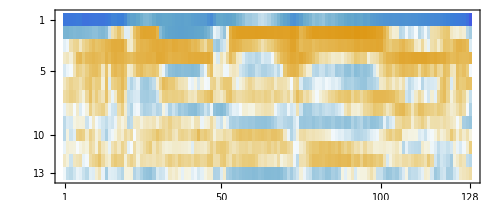
-Graphics-AudioMFCC

```mathematica
Labeled[MatrixPlot[Transpose@Normal[NetEncoder["AudioMFCC"][audioSpanish]]],"AudioMFCC"]
```